# Homework 1

## By Marvyn Bailly

## Question 1

```mathematica
pi0[t_] = 1;
pi1[t_] = 2t-1;
pi2[t_] = 3/2(2t -1)^2 - 1/2;
f[t_] = Exp[-t];
```

```mathematica
c0 = Integrate[pi0[t]f[t],{t,0,1}]/Integrate[pi0[t]*pi0[t],{t,0,1}]
c1 = Integrate[pi1[t]f[t],{t,0,1}]/Integrate[pi1[t]*pi1[t],{t,0,1}]
c2 = Integrate[pi2[t]f[t],{t,0,1}]/Integrate[pi2[t]*pi2[t],{t,0,1}]
```

(-1+ⅇ)/ⅇ

(3 (-3+ⅇ))/ⅇ

5 (7-19/ⅇ)

```mathematica
p2[t_] = c0*pi0[t] + c1*pi1[t] + c2*pi2[t]
Collect[FullSimplify[p2[t]],t]
```

(-1+ⅇ)/ⅇ+(3 (-3+ⅇ) (-1+2 t))/ⅇ+5 (7-19/ⅇ) (-1/2+3/2 (-1+2 t)^2)

(-87+33 ⅇ)/ⅇ+((552-204 ⅇ) t)/ⅇ+((-570+210 ⅇ) t^2)/ⅇ

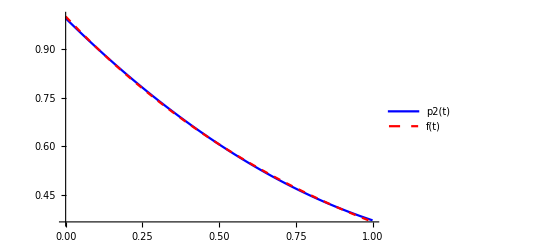

```mathematica
Plot[{p2[t],f[t]},{t,0,1},PlotStyle->{Blue,{Red,Dashed}},PlotLegends->"Expressions" ]
```

### Question 2

```mathematica
data1 = {{-1,1},{0,1},{1,2},{2,0}};
data2 ={-1,0,1,2};
data3 = {1,1,2,0};
```

#### Part a

```mathematica
A= {{1,-1,1,-1},{1,0,0,0},{1,1,1,1},{1,2,4,8}};
b = Transpose[{1,1,2,0}];
c = Transpose[{c0,c1,c2,c3}];
solutions = Solve[A.c == b,c]
p1 = Sum[(c/. solutions[[1]])[[i+1]]x^i,{i,0,3}]
```

{{c0→1,c1→7/6,c2→1/2,c3→-2/3}}

1+(7 x)/6+x^2/2-(2 x^3)/3

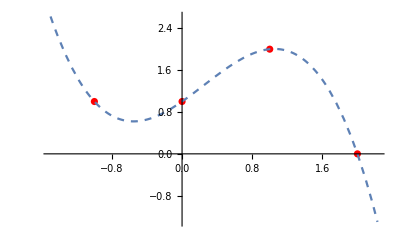

```mathematica
Show[ListPlot[data1,PlotStyle->{Red,Large}],Plot[p1,{x,-1.5,2.5},PlotStyle->Dashed],PlotRange-> All]
```

#### Part B

```mathematica
Clear[A,b,c]
L = {l0,l1,l2,l3};
For[i=0,i<=3,i++,
	L[[i+1]]=Product[(x - j)/(data2[[i+1]]- j),{j,Delete[data2,i+1]}]
]
L
p2 = Sum[data3[[j+1]]*L[[j+1]],{j,0,3}]
Expand[p2]
```

{-1/6 (1-x) (2-x) x,1/2 (1-x) (2-x) (1+x),1/2 (2-x) x (1+x),1/6 (-1+x) x (1+x)}

-1/6 (1-x) (2-x) x+1/2 (1-x) (2-x) (1+x)+(2-x) x (1+x)

1+(7 x)/6+x^2/2-(2 x^3)/3

#### Part C

```mathematica
Expand[1 + 0 + 1/2(x)(x+1) - 2/3(x)(x-1)(x+1)]
```

1+(7 x)/6+x^2/2-(2 x^3)/3

### Question 3

1+x-2 (-1+x) x+2/3 (-1+x)^2 x+5/36 (-3+x) (-1+x)^2 x

1+(13 x)/4-(85 x^2)/36-x^3/36+(5 x^4)/36

1/18

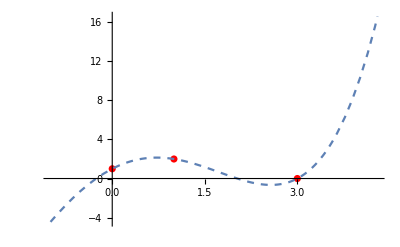

```mathematica
p4[x_] = 1 + 1(x) -2(x)(x-1)+2/3(x)(x-1)^2 +5/36(x)(x-1)^2(x-3)
Expand[p4[x]]
p4[2]
Show[ListPlot[{{0,1},{1,2},{3,0}},PlotStyle->Red],Plot[p4[x],{x,-1,5},PlotStyle->Dashed],PlotRange-> All]
```